

```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

```mathematica
cosy[labels_,labelstyle_]:=Flatten@{Arrow[{{0,0,0},{1,0,0}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{0,0,1}}],labelstyle,Text[labels[[1]],{1.1,0,0}],Text[labels[[2]],{0,1.1,0}],Text[labels[[3]],{0,0,1.1}]};
Graphics3D[{{(*Coordinate system 1*)cosy[{"X","Y","Z"},Darker@Orange],Darker@Orange,Text["World",{-.3,-.3,.5}]},{(*Coordinate system 2*)Rotate[cosy[{"x","y","z"},Blue],-30 °,{-1,0,1}]~Translate~{0,0,-2}},{(*Connecting arrow*)Darker@Green,Arrow[{{0,0,0},{0,0,-2}}],Text["C(t)",{0,-.2,-1}]},{(*Red stuff*)Red,Arrow[{{0,0,0},{0,3,-1}}],Arrow[{{0,0,-2},{0,3,-1}}],Text["\!\(\*SubscriptBox[\(p\), \(world\)]\)",1/2 {0,3,-1}+{0,0,.5}],Text["\!\(\*SubscriptBox[\(p\), \(0\)]\)",1/2 {0,3,-1}+{0,0,-1.5}],Text["p(t)",{0,3,-1}+{0,.5,0}]}},Boxed->False]
```

-Graphics3D-

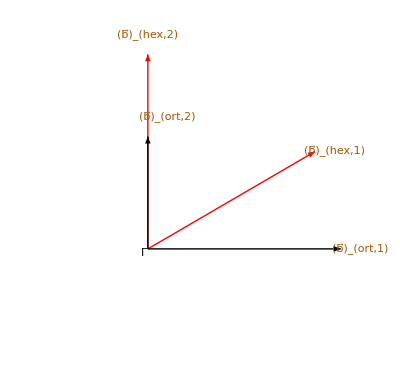

```mathematica
CoordinateSystem[origin_,Xdirection_,Ydirection_,labels_,labelposition_,labelstyle_,labelsize_]:=
{Arrow[{origin,Xdirection}],Arrow[{origin,Ydirection}],labelstyle,Text[labels[[1]],labelposition[[1]]],Text[labels[[2]],labelposition[[2]]]};
BrillouinZone[nodeset_]:=
{Polygon[nodeset]};
Graphics[{{(*Reciprocal lattice of 2D hexagonal system*)
Red,CoordinateSystem[{0,0},{√3/2,1/2},{0,1},{Subscript[OverVector[b],hex,1],Subscript[OverVector[b],hex,2]},{{√3/2+0.1,1/2},{0,1.1}},Darker@Orange]},
{(*First Brillouin zone of 2D hexagonal system*)
EdgeForm[Red],Opacity[0],BrillouinZone[Table[{√3*Cos[2*Pi*k/6]/3,√3*Sin[2*Pi*k/6]/3},{k,6}]]},
{(*Reciprocal lattice of 2D orthogonal system*)
Black,CoordinateSystem[{0,0},{1,0},{0,√3/3},{Subscript[OverVector[b],ort,1],Subscript[OverVector[b],ort,2]},{{1.1,0},{0.1,√3/3+0.1}},Darker@Orange]},
{(*First Brillouin zone of 2D orthogonal system*)
EdgeForm[Black],Opacity[0],BrillouinZone[{{1/2,√3/6},{1/2,-√3/6},{-1/2,-√3/6},{-1/2,√3/6}}]},
(*Gamma*)Text[Γ,{-0.02,-0.02}]},
Boxed->False]
```

```mathematica
Table[Text[Style["ABC",FontSize->p]],{p,{12,24,36}}]
```

{ABC,ABC,ABC}

```mathematica
h[x_,y_]:=Polygon[Table[{Cos[2 Pi k/6]+x,Sin[2 Pi k/6]+y},{k,6}]]
```